```mathematica
M[k_]:=2*Sum[(-1)^i*Binomial[k,i]/(2*i+1),{i,0,k}];
k∈Integers&&k≥2;
Plot[M[k], {k, 2, +10}, PlotRange->{0, 2}, PlotStyle ->{Line->Point, Directive[Black,Thickness[0.004]]}, AxesLabel->{k, M}, Background->Hue[0,0,1], Ticks->{{ 2, 3, 4}, { 1}}, AxesStyle->Directive[Thickness[0.0042]], TicksStyle->Directive[Black,FontSize->11, Thick], LabelStyle->Directive[Black,Bold, FontSize->13],PlotLegends->Placed[{"V1"},{After,Center}]]
```

Plot::itraw: Raw object k∈ cannot be used as an iterator.

Plot[M[k],{k∈ℤ,2,+10},PlotRange→{0,2},PlotStyle→{Line→Point,Directive[Black,Thickness[0.004]]},AxesLabel→{k,M},Background→Hue[0, 0, 1],Ticks→{{2,3,4},{1}},AxesStyle→Directive[Thickness[0.0042]],TicksStyle→Directive[Black,FontSize→11,Thick],LabelStyle→Directive[Black,Bold,FontSize→13],PlotLegends→Placed[{V1},{After,Center}]]

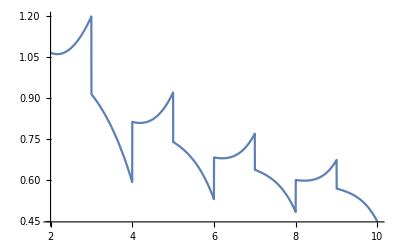

```mathematica
Plot[M[k], {k, 2, +10}]
```